```mathematica
Needs["ErrorBarPlots`"]
```

## Linear Fit of PT Data

```mathematica
PTdata=Import["F:\\Fahad Documents\\Dept. of Physics,SUST\\Study Materials\\4-2\\PROJECT PHY428-20220803T021501Z-001\\PROJECT PHY428\\Figures\\PTdata combined.csv"]
```

{{Q^2,muR,error_muR,},{0.49,0.966,0.033,MK Jones},{0.79,0.95,0.032,},{1.18,0.869,0.041,},{1.48,0.798,0.068,},{1.77,0.728,0.073,},{1.88,0.72,0.091,},{2.47,0.726,0.089,},{2.97,0.612,0.088,},{3.47,0.609,0.092,},{0.32,0.93,0.074,O.Gayou},{0.35,0.91,0.065,},{0.39,0.961,0.038,},{0.46,0.952,0.04,},{0.57,0.959,0.046,},{0.76,0.966,0.045,},{0.86,0.865,0.044,},{0.88,0.923,0.099,},{1.02,0.9,0.06,},{1.12,0.825,0.047,},{1.18,0.851,0.073,},{1.42,0.733,0.087,},{1.76,0.816,0.184,},{0.8,0.901,0.17,M.Paolone},{1.3,0.858,0.27,},{0.5,0.895,0.063,S. Strauch},{1,0.868,0.049,},{1.6,0.992,0.05,},{2.6,0.869,0.18,},{3.5,0.571,0.079,A. J. R. Puckett},{4,0.517,0.064,},{4.8,0.45,0.064,},{5.6,0.354,0.104,}}

```mathematica
TableForm[PTdata]
```

Q^2 | muR | error_muR | 
0.49 | 0.966 | 0.033 | MK Jones
0.79 | 0.95 | 0.032 | 
1.18 | 0.869 | 0.041 | 
1.48 | 0.798 | 0.068 | 
1.77 | 0.728 | 0.073 | 
1.88 | 0.72 | 0.091 | 
2.47 | 0.726 | 0.089 | 
2.97 | 0.612 | 0.088 | 
3.47 | 0.609 | 0.092 | 
0.32 | 0.93 | 0.074 | O.Gayou
0.35 | 0.91 | 0.065 | 
0.39 | 0.961 | 0.038 | 
0.46 | 0.952 | 0.04 | 
0.57 | 0.959 | 0.046 | 
0.76 | 0.966 | 0.045 | 
0.86 | 0.865 | 0.044 | 
0.88 | 0.923 | 0.099 | 
1.02 | 0.9 | 0.06 | 
1.12 | 0.825 | 0.047 | 
1.18 | 0.851 | 0.073 | 
1.42 | 0.733 | 0.087 | 
1.76 | 0.816 | 0.184 | 
0.8 | 0.901 | 0.17 | M.Paolone
1.3 | 0.858 | 0.27 | 
0.5 | 0.895 | 0.063 | S. Strauch
1 | 0.868 | 0.049 | 
1.6 | 0.992 | 0.05 | 
2.6 | 0.869 | 0.18 | 
3.5 | 0.571 | 0.079 | A. J. R. Puckett
4 | 0.517 | 0.064 | 
4.8 | 0.45 | 0.064 | 
5.6 | 0.354 | 0.104 |

```mathematica
Transpose[%6]
```

{{Q^2,0.49,0.79,1.18,1.48,1.77,1.88,2.47,2.97,3.47,0.32,0.35,0.39,0.46,0.57,0.76,0.86,0.88,1.02,1.12,1.18,1.42,1.76,0.8,1.3,0.5,1,1.6,2.6,3.5,4,4.8,5.6},{muR,0.966,0.95,0.869,0.798,0.728,0.72,0.726,0.612,0.609,0.93,0.91,0.961,0.952,0.959,0.966,0.865,0.923,0.9,0.825,0.851,0.733,0.816,0.901,0.858,0.895,0.868,0.992,0.869,0.571,0.517,0.45,0.354},{error_muR,0.033,0.032,0.041,0.068,0.073,0.091,0.089,0.088,0.092,0.074,0.065,0.038,0.04,0.046,0.045,0.044,0.099,0.06,0.047,0.073,0.087,0.184,0.17,0.27,0.063,0.049,0.05,0.18,0.079,0.064,0.064,0.104},{,MK Jones,,,,,,,,,O.Gayou,,,,,,,,,,,,,M.Paolone,,S. Strauch,,,,A. J. R. Puckett,,,}}

```mathematica
PTQ2data={0.49,0.79,1.18,1.48,1.77,1.88,2.47,2.97,3.47,0.32,0.35,0.39,0.46,0.57,0.76,0.86,0.88,1.02,1.12,1.18,1.42,1.76,0.8,1.3,0.5,1,1.6,2.6,3.5,4,4.8,5.6}
PTmuRdata={0.966,0.95,0.869,0.798,0.728,0.72,0.726,0.612,0.609,0.93,0.91,0.961,0.952,0.959,0.966,0.865,0.923,0.9,0.825,0.851,0.733,0.816,0.901,0.858,0.895,0.868,0.992,0.869,0.571,0.517,0.45,0.354}
PTmuRerrordata={0.033,0.032,0.041,0.068,0.073,0.091,0.089,0.088,0.092,0.074,0.065,0.038,0.04,0.046,0.045,0.044,0.099,0.06,0.047,0.073,0.087,0.184,0.17,0.27,0.063,0.049,0.05,0.18,0.079,0.064,0.064,0.104}
PTdata=Transpose[{PTQ2data, PTmuRdata}]
PTerrorplot = Transpose[{PTQ2data, PTmuRdata, PTmuRerrordata}]
y=1-a*Q2
FindFit[PTdata,{y},{a},Q2]
```

{0.49,0.79,1.18,1.48,1.77,1.88,2.47,2.97,3.47,0.32,0.35,0.39,0.46,0.57,0.76,0.86,0.88,1.02,1.12,1.18,1.42,1.76,0.8,1.3,0.5,1,1.6,2.6,3.5,4,4.8,5.6}

{0.966,0.95,0.869,0.798,0.728,0.72,0.726,0.612,0.609,0.93,0.91,0.961,0.952,0.959,0.966,0.865,0.923,0.9,0.825,0.851,0.733,0.816,0.901,0.858,0.895,0.868,0.992,0.869,0.571,0.517,0.45,0.354}

{0.033,0.032,0.041,0.068,0.073,0.091,0.089,0.088,0.092,0.074,0.065,0.038,0.04,0.046,0.045,0.044,0.099,0.06,0.047,0.073,0.087,0.184,0.17,0.27,0.063,0.049,0.05,0.18,0.079,0.064,0.064,0.104}

{{0.49,0.966},{0.79,0.95},{1.18,0.869},{1.48,0.798},{1.77,0.728},{1.88,0.72},{2.47,0.726},{2.97,0.612},{3.47,0.609},{0.32,0.93},{0.35,0.91},{0.39,0.961},{0.46,0.952},{0.57,0.959},{0.76,0.966},{0.86,0.865},{0.88,0.923},{1.02,0.9},{1.12,0.825},{1.18,0.851},{1.42,0.733},{1.76,0.816},{0.8,0.901},{1.3,0.858},{0.5,0.895},{1,0.868},{1.6,0.992},{2.6,0.869},{3.5,0.571},{4,0.517},{4.8,0.45},{5.6,0.354}}

{{0.49,0.966,0.033},{0.79,0.95,0.032},{1.18,0.869,0.041},{1.48,0.798,0.068},{1.77,0.728,0.073},{1.88,0.72,0.091},{2.47,0.726,0.089},{2.97,0.612,0.088},{3.47,0.609,0.092},{0.32,0.93,0.074},{0.35,0.91,0.065},{0.39,0.961,0.038},{0.46,0.952,0.04},{0.57,0.959,0.046},{0.76,0.966,0.045},{0.86,0.865,0.044},{0.88,0.923,0.099},{1.02,0.9,0.06},{1.12,0.825,0.047},{1.18,0.851,0.073},{1.42,0.733,0.087},{1.76,0.816,0.184},{0.8,0.901,0.17},{1.3,0.858,0.27},{0.5,0.895,0.063},{1,0.868,0.049},{1.6,0.992,0.05},{2.6,0.869,0.18},{3.5,0.571,0.079},{4,0.517,0.064},{4.8,0.45,0.064},{5.6,0.354,0.104}}

1-a Q2

{a→0.114811}

## Bosted fit R_FF

```mathematica
Q2=1.45
z=Sqrt[Q2]
tau=Q2/(4*0.938)
GEbosted= 1/(1+0.62*z+0.68*z^2+2.80*z^3+0.83*z^4)
GMbosted=2.7972*(1/(1+0.35*z+2.44*z^2+0.50*z^3+1.04*z^4+0.34*z^5))
Rffbosted=2.7972*GEbosted/GMbosted
RffPT=1-0.12*Q2
```

1.45

1.20416

0.386461

0.106763

0.315005

0.948041

0.826

```mathematica
deltabosted= ((2.7972*GEbosted)^2-(GMbosted*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammabosted=1+ ((2*deltabosted*(1-eps))/(GMbosted^2+(eps/tau)*GEbosted^2))
```

0.00579682

1+(0.0115936 (1-eps))/(0.099228+0.0294942 eps)

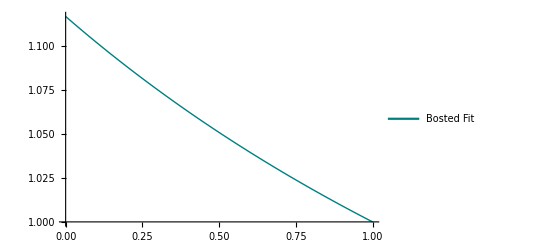

```mathematica
Pboosted=Plot[R2gammabosted,{eps,0,1},PlotStyle->{Blend[{Green,Blue}],Thick},PlotLegends-> Placed[LineLegend[{"Bosted Fit"}],{0.65,0.85}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## Arrington Fit R_FF

```mathematica
x=Q2
Q2=1.45
GEarr=1/(1+3.226*x+1.508*x^2-0.3773*x^3+0.611*x^4-0.185*x^5)
GMarr=2.7972*(1/(1+3.19*x+1.355*x^2+0.151*x^3-1.14*10^-2*x^4+5.33*10^-4x^5-9*10^-6x^6))
Rffarrington= 2.7972*GEarr/GMarr
```

1.45

1.45

0.10854

0.314728

0.964672

```mathematica
deltaarr =((2.7972*GEarr)^2-(GMarr*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaarr=1+ ((2*deltaarr*(1-eps))/(GMarr^2+(eps/tau)*GEarr^2))
```

0.00663685

1+(0.0132737 (1-eps))/(0.0990538+0.0304844 eps)

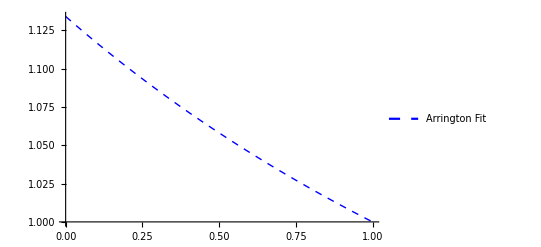

```mathematica
Parrington=Plot[R2gammaarr,{eps,0,1},PlotStyle->{Blue,Dashed,Thick},PlotLegends-> Placed[LineLegend[{"Arrington Fit"}],{0.65,0.75}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## Standard Dipole Fit

```mathematica
GEdipole=1/(1+(Q2/0.71))^2
GMdipole=2.7972*(1/(1+(Q2/0.71))^2)
deltadipole =((2.7972*GEdipole)^2-(GMdipole*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammadipole=1+ ((2*deltadipole*(1-eps))/(GMdipole^2+(eps/tau)*GEdipole^2))
```

0.108046

0.302227

0.00783072

1+(0.0156614 (1-eps))/(0.0913409+0.0302074 eps)

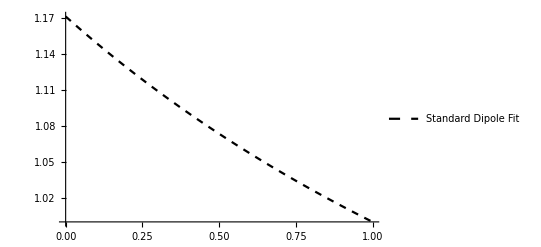

```mathematica
Dipoleplot=Plot[R2gammadipole,{eps,0,1},PlotStyle->{Black,Dashed},PlotLegends-> Placed[LineLegend[{"Standard Dipole Fit"}],{0.7,0.55}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## Bernauer Fit(using Pade Model)

```mathematica
a1=3.439
a2=-1.602
a3=0.068
b1=15.055
b2=48.061
b3=99.304
b4=0.012
b5=8.650
c1=-1.465
c2=1.260
c3=0.262
d1=9.627
d2=0.000
d3=0.000
d4=11.179
d5=13.245
Q2=1.45
GEpade= (1+a1*tau+a2*tau^2+a3*tau^3)/(1+b1*tau+b2*tau^2+b3*tau^3+b4*tau^4+b5*tau^5)
GMpade= 2.7972*((1+c1*tau+c2*tau^2+c3*tau^3)/(1+d1*tau+d2*tau^2+d3*tau^3+d4*tau^4+d5*tau^5))
tau=Q2/(4*0.938^2)
RffPT=1-0.12*Q2
deltaBern=((2.7972*GEpade)^2-(GMpade*RffPT)^2)/(RffPT^2+tau*2.7972^2)
R2gammaBern=1+ ((2*deltaBern*(1-eps))/(GMpade^2+(eps/tau)*GEpade^2))
```

3.439

-1.602

0.068

15.055

48.061

99.304

0.012

8.65

-1.465

1.26

0.262

9.627

0.

0.

11.179

13.245

1.45

0.0959302

0.32289

0.412005

0.826

0.000223068

1+(0.000446135 (1-eps))/(0.104258+0.0223361 eps)

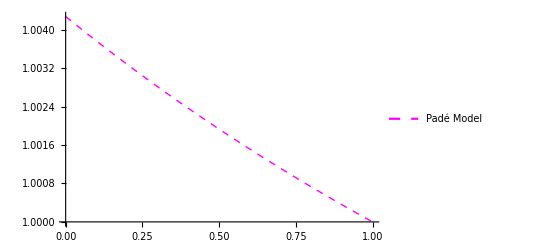

```mathematica
PltBernauer=Plot[R2gammaBern,{eps,0,1},PlotStyle->{Magenta,Dashed,Thick},PlotLegends-> Placed[LineLegend[{"Padé Model"}],{0.65,0.65}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## Graph of R_(2γ) vs ε using suitable fit

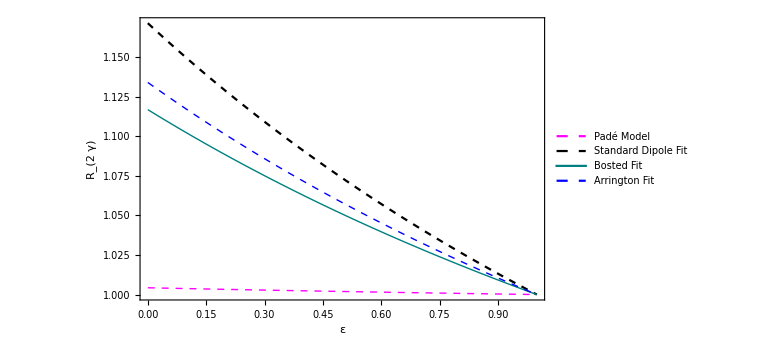

```mathematica
Show[PltBernauer,Dipoleplot,Pboosted,Parrington,PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["ε",Bold,18],Style["R_(2  γ)",Bold,18]},  ImageSize-> Large]
```

## CLAS Experiment

```mathematica
CLASdata=Import["F:\\Fahad Documents\\Dept. of Physics,SUST\\Study Materials\\4-2\\PROJECT PHY428-20220803T021501Z-001\\PROJECT PHY428\\Figures\\CLAS Data(Rimal).csv"]
```

{{Q^2,epsilon,R_2gamma,total error(R_2gamma)},{0.84,0.39,1.007,0.0223},{0.86,0.52,0.9896,0.122},{0.85,0.83,1.0074,0.0055},{0.85,0.91,0.9976,0.0047},{1.44,0.4,1.0282,0.0075},{1.45,0.6,1.0047,0.007},{1.46,0.76,0.9943,0.0075},{1.47,0.83,0.9956,0.0056},{1.47,0.9,0.9965,0.0072},{0.72,0.45,1.0052,0.0058},{0.89,0.45,1.0009,0.0132},{1.14,0.45,1.0239,0.0078},{1.73,0.45,1.0176,0.0113},{0.23,0.92,0.992,0.0052},{0.34,0.89,0.9888,0.0043},{0.45,0.89,0.9974,0.0043},{0.63,0.89,1.0025,0.0059},{0.89,0.88,1.0097,0.0049},{1.42,0.87,1,0.0057}}

```mathematica
TableForm[CLASdata]
```

Q^2 | epsilon | R_2gamma | total error(R_2gamma)
0.84 | 0.39 | 1.007 | 0.0223
0.86 | 0.52 | 0.9896 | 0.122
0.85 | 0.83 | 1.0074 | 0.0055
0.85 | 0.91 | 0.9976 | 0.0047
1.44 | 0.4 | 1.0282 | 0.0075
1.45 | 0.6 | 1.0047 | 0.007
1.46 | 0.76 | 0.9943 | 0.0075
1.47 | 0.83 | 0.9956 | 0.0056
1.47 | 0.9 | 0.9965 | 0.0072
0.72 | 0.45 | 1.0052 | 0.0058
0.89 | 0.45 | 1.0009 | 0.0132
1.14 | 0.45 | 1.0239 | 0.0078
1.73 | 0.45 | 1.0176 | 0.0113
0.23 | 0.92 | 0.992 | 0.0052
0.34 | 0.89 | 0.9888 | 0.0043
0.45 | 0.89 | 0.9974 | 0.0043
0.63 | 0.89 | 1.0025 | 0.0059
0.89 | 0.88 | 1.0097 | 0.0049
1.42 | 0.87 | 1 | 0.0057

```mathematica
Transpose[%2]
```

{{Q^2,0.84,0.86,0.85,0.85,1.44,1.45,1.46,1.47,1.47,0.72,0.89,1.14,1.73,0.23,0.34,0.45,0.63,0.89,1.42},{epsilon,0.39,0.52,0.83,0.91,0.4,0.6,0.76,0.83,0.9,0.45,0.45,0.45,0.45,0.92,0.89,0.89,0.89,0.88,0.87},{R_2gamma,1.007,0.9896,1.0074,0.9976,1.0282,1.0047,0.9943,0.9956,0.9965,1.0052,1.0009,1.0239,1.0176,0.992,0.9888,0.9974,1.0025,1.0097,1},{total error(R_2gamma),0.0223,0.122,0.0055,0.0047,0.0075,0.007,0.0075,0.0056,0.0072,0.0058,0.0132,0.0078,0.0113,0.0052,0.0043,0.0043,0.0059,0.0049,0.0057}}

```mathematica
epsdataC={0.4,0.6,0.76,0.83,0.9}
R2gammadataC={1.0282,1.0047,0.9943,0.9956,0.9965}
R2gammaerrorC={0.0075,0.007,0.0075,0.0056,0.0072}
dataCLAS=Transpose[{epsdataC, R2gammadataC}]
errorplotCLAS= Transpose[{epsdataC, R2gammadataC, R2gammaerrorC}]
```

{0.4,0.6,0.76,0.83,0.9}

{1.0282,1.0047,0.9943,0.9956,0.9965}

{0.0075,0.007,0.0075,0.0056,0.0072}

{{0.4,1.0282},{0.6,1.0047},{0.76,0.9943},{0.83,0.9956},{0.9,0.9965}}

{{0.4,1.0282,0.0075},{0.6,1.0047,0.007},{0.76,0.9943,0.0075},{0.83,0.9956,0.0056},{0.9,0.9965,0.0072}}

## Combined with CLAS data: Graph of R_(2γ) vs ε using suitable fit

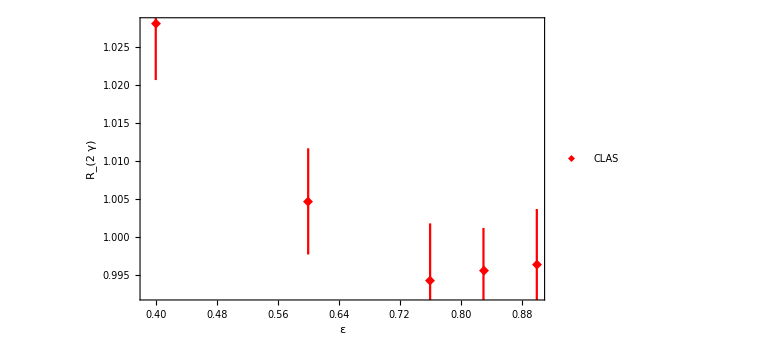

```mathematica
pltCLAS=ErrorListPlot[Table[{errorplotCLAS[[i,{1,2}]],ErrorBar[errorplotCLAS[[i,3]]]},{i,1,Length[errorplotCLAS]}], PlotStyle->Red,Joined->False,PlotMarkers->{"◆", Medium}, FrameLabel->{Style["ε",Bold,18],Style["R_(2  γ)",Bold,18]},PlotLegends-> Placed[LineLegend[{"CLAS"}],{0.65,0.95}], Frame-> True,FrameTicks->All,LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16], ImageSize-> Large]
```

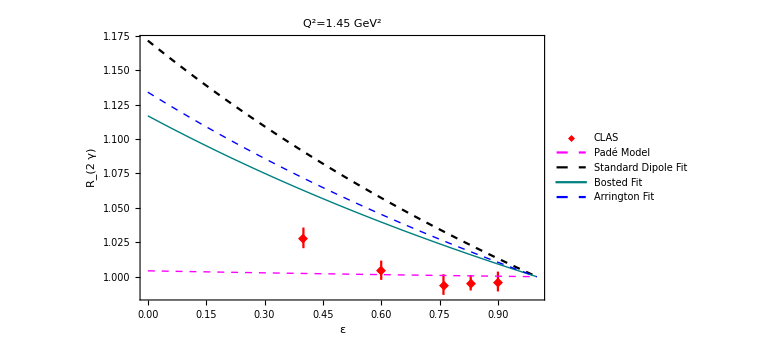

```mathematica
Show[pltCLAS,PltBernauer,Dipoleplot,Pboosted,Parrington,PlotRange->All,Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2=1.45 GeV^2",Bold,Black],FrameLabel->{Style["ε",Bold,22,Black],Style["R_(2  γ)",Bold,20,Black]},Axes-> False,LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14],FrameTicksStyle-> Directive[Black,14],  ImageSize-> Large]
```